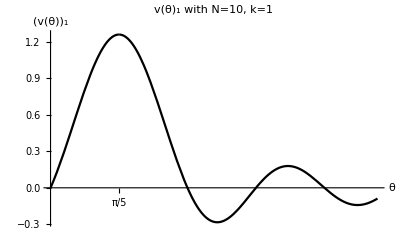

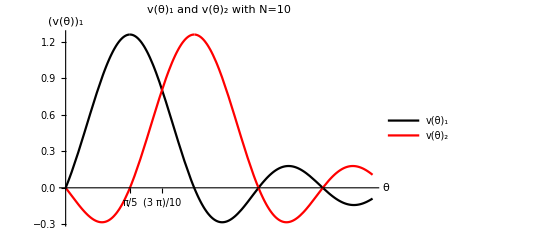

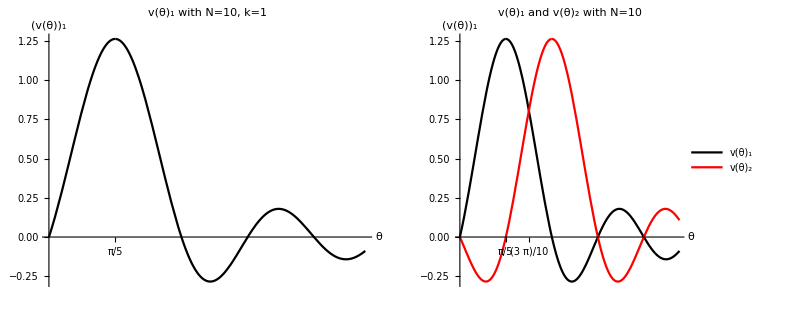

```mathematica
v[k_, t_, n_]:= (2 Pi n)^(-1/2)Sin[n/2(t-(2 Pi k)/n)]/Sin[1/2(t-(2 Pi k)/n)]
plot1 = Plot[{v[1,t,10],Line[{{1,1},{2,2}}]},{t,0,3}, PlotStyle->Black, AxesLabel->{θ,Subscript[v[θ], 1]}, PlotLabel-> "v(θ)_1 with N=10, k=1", Ticks -> {{2Pi/10},None}, ImagePadding->20]
plot2 = Plot[{v[1,t,10],v[2,t,10]},{t,0,3},PlotStyle->{Black,Red},AxesLabel->{θ,Subscript[v[θ], k]},PlotLabel->"v(θ)_1 and v(θ)_2 with N=10", Ticks->{{2Pi/10,3Pi/10},None},PlotLegends->Placed[{"v(θ)_1", "v(θ)_2"},{Right,Top}],ImagePadding->20]
GraphicsRow[{plot1,plot2}]
```

```mathematica
Export["/Users/jamespuleston/Documents/Cambridge/Essay/TunnellingTimesInQuantumMechanics/Mathematica/plot1.pdf",GraphicsRow[{plot1,plot2}]]
```

/Users/jamespuleston/Documents/Cambridge/Essay/TunnellingTimesInQuantumMechanics/Mathematica/plot1.pdf